```mathematica
MakeInnerOuterGraphBound[counts_]:=Block[{len=Length[counts],result, current,previous=-1, inner=1,zone},
result={};
current=len+1;
For[inner=1,inner≤len,inner++,
AppendTo[result,current];
For[zone=0,zone≤counts[[inner]],zone++,
previous=current;
current++;
];
];
result
]
```

```mathematica
HandleSolutions[n_,p_]:=Block[{graphParm=PadLeft[IntegerDigits[n,p],5], g, constraints, bounds},
g=Graph[MakeInnerOuterGraph[graphParm]];
bounds=Map[Symbol["x"<>ToString[#]]&, MakeInnerOuterGraphBound[graphParm]];
constraints=bounds[[1]]==1&&bounds[[2]]==2&&bounds[[3]]==3&&bounds[[4]]==2&&bounds[[5]]==3;
With[{result=
Table[
Length[GraphSolutions3[g, h&& constraints]]
,{h,{True,((x1==x3)&&(x2==x4)),
((x2==x4)&&(x3==x5)),
((x3==x5)&&(x4==x1)),
((x4==x1)&&(x5==x2)),
((x5==x2)&&(x1==x3))}}
]},
PrintTemporary[result];
If[Rest[result]=={0,0,0,0,0},Print[{n,p} ]];
result
]
]
```

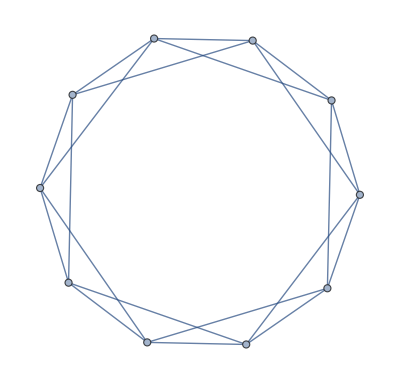
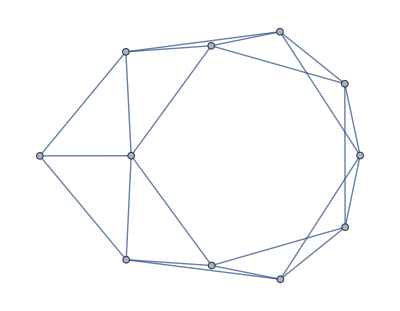
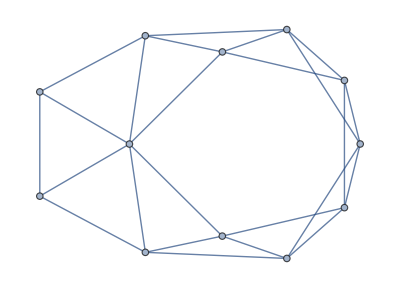
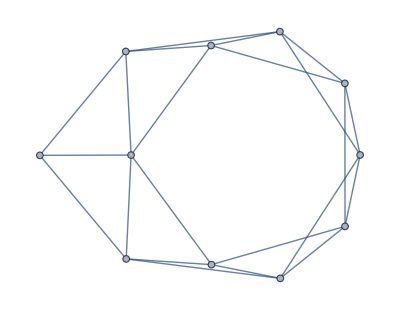
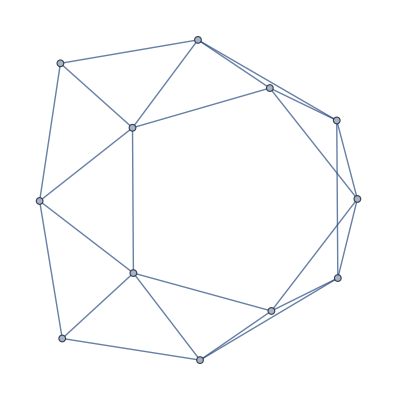
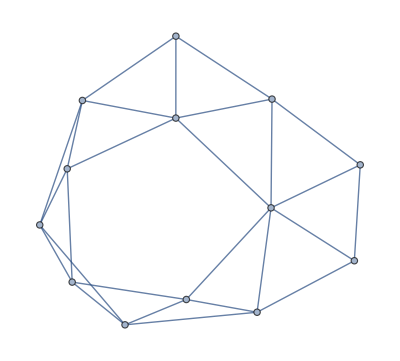
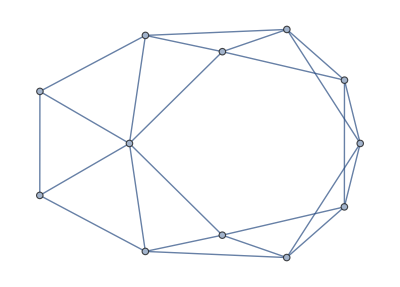
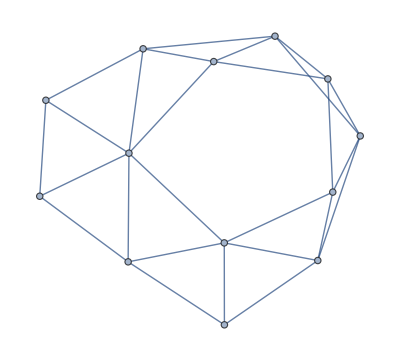
{{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{4,1,1,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{12,3,3,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{36,9,9,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{108,27,27,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{324,81,81,0,0,0},-Graphics-},{{972,243,243,0,0,0},-Graphics-}}

```mathematica
With[{exp=3},Monitor[Table[HandleSolutions[k,exp],{k,0,exp^5-1}],{k,exp^5}]]
```

```mathematica
With[{exp=4},Monitor[Table[HandleSolutions[k,exp],{k,0,exp^5-1}],{k,exp^5}]]
```

$Aborted